```mathematica
SetDirectory[NotebookDirectory[]];
fRand[aXorY_,aRho_]:=RandomVariate[NormalDistribution[5+aRho(aXorY-5),1-aRho^2],{1}][[1]]
fStep[aXInd_Integer,aX_,aY_,aRho_]:=If[aXInd==1,{0,fRand[aY,aRho],aY},{1,aX,fRand[aX,aRho]}]
fGibbs[aNumIterations_Integer,aXStart_,aYStart_,aRho_]:=NestList[fStep[#[[1]],#[[2]],#[[3]],aRho]&,{1,aXStart,aYStart},aNumIterations][[All,2;;3]]
fRandReparameter[aCOrU_Integer,aRho_]:=RandomVariate[NormalDistribution[If[aCOrU==1,0,10],If[aCOrU==1,2(1-aRho),2(1+aRho)]],{1}][[1]]
fStepReparameter[aXInd_Integer,aX_,aY_,aRho_]:=If[aXInd==1,{0,fRandReparameter[1,aRho],aY},{1,aX,fRandReparameter[0,aRho]}]
fGibbsReparameter[aNumIterations_Integer,aXStart_,aYStart_,aRho_]:=NestList[fStepReparameter[#[[1]],#[[2]],#[[3]],aRho]&,{1,aXStart,aYStart},aNumIterations][[All,2;;3]]
fRetransformedGibbs[aNumIterations_Integer,aXStart_,aYStart_,aRho_]:=Module[{lReparam=fGibbsReparameter[aNumIterations,aXStart,aYStart,aRho]},{{1/2,1/2},{-1/2,1/2}} .#&/@lReparam]
fPDF[x_,y_,aRho_]:=PDF[MultinormalDistribution[{5,5},{{1,aRho},{aRho,1}}],{x,y}]
```

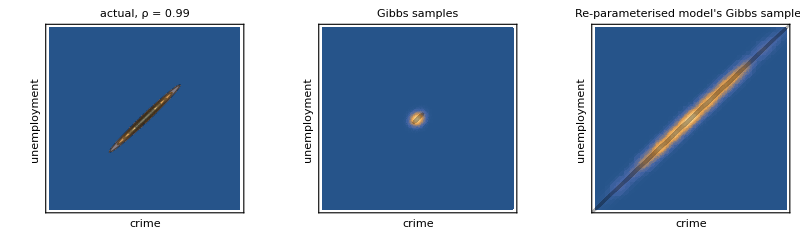

```mathematica
n1=1000;
lNumSamplesGibbs=fGibbs[n1,5,5,0.99];
lNumSamplesGibbsReparam=fRetransformedGibbs[n1,0,10,0.99];
g1=ContourPlot[fRand[x,y,0.99],{x,0,10},{y,0,10},PlotRange->bPlotRange, PerformanceGoal->"Quality",FrameTicks->None,Frame->{True,True,False,False},FrameLabel->{"crime","unemployment"},PlotLabel->"actual, ρ = 0.99"];
g2=Show[SmoothDensityHistogram[lNumSamplesGibbs,0.2,PlotRange->{{0,10},{0,10}},FrameTicks->None,Frame->{True,True,False,False},FrameLabel->{"crime","unemployment"},Mesh->10,PlotLabel->"Gibbs samples"],ListLinePlot[lNumSamplesGibbs,PlotStyle->Opacity[0.3,Black]]];
g3=Show[SmoothDensityHistogram[lNumSamplesGibbsReparam,0.2,PlotRange->{{0,10},{0,10}},FrameTicks->None,Frame->{True,True,False,False},FrameLabel->{"crime","unemployment"},Mesh->10,PlotLabel->"Re-parameterised model's Gibbs samples"],ListLinePlot[lNumSamplesGibbsReparam,PlotStyle->Opacity[0.3,Black]]];
gFinal=Show[GraphicsRow[{g1,g2,g3}],ImageSize->800]
```

```mathematica
Export["Gibbs_reparametersCrime.png",gFinal]
```

Gibbs_reparametersCrime.png